```mathematica
(*Dr. Maseim B. Kenmoe, 08.09.2025, Regensburg*)
```

```mathematica
(*-Graphics--Graphics-*)

(*As far as these numerical tests are concerned, we have always chosen the amplitude A and the frequency w such that A/w<<1*)
```

```mathematica
-Graphics-
where
-Graphics-
and

-Graphics-
```

```mathematica
(*-Graphics-*)
eq1[A_,A0_,ω_,ω0_,ϕ_,D1_,Δ_]:=ⅈ y1'[τ]-1/2(α τ+A  Cos[ω τ]+D1) y1[τ]-1/2(Δ+A0  Cos[ω0 τ+ϕ])y2[τ];

eq2[A_,A0_,ω_,ω0_,ϕ_,D1_,Δ_]:=ⅈ y2'[τ]-1/2(-α τ-A  Cos[ω τ]-D1)y2[τ]-1/2(Δ+A0  Cos[ω0 τ+ϕ])y1[τ];
```

```mathematica
(*-Graphics-*)
y10=1;
y20=0;
α :=1;
A0:=0.8;
A:=2.9;
ω:=100;
ω0:=1;
ϕ:=Pi/2;
Δ:=0.075;
D1:=1.5;
τin=-50;
τfin=50;
```

```mathematica
(*-Graphics-*)
int[A_,A0_,ω_,ω0_, ϕ_,D1_,Δ_]:=Module[{sol},sol=NDSolve[{eq1[A,A0,ω,ω0, ϕ,D1,Δ]==0,eq2[A,A0,ω,ω0, ϕ,D1,Δ]==0,y1[τ0]==y10,y2[τ0]==y20},{y1,y2},{τ,τin,τfin},MaxSteps->100000000][[1]];
Return[{y1/.sol,y2/.sol}];]
```

```mathematica
(*-Graphics-*)
P11[τ_,A_,A0_,ω_,ω0_, ϕ_,D1_,Δ_]:=(Re[int[A,A0,ω,ω0, ϕ,D1,Δ][[1]][τ]])^2+(Im[int[A,A0,ω,ω0, ϕ,D1,Δ][[1]][τ]])^2;

P22[τ_,A_,A0_,ω_,ω0_, ϕ_,D1_,Δ_]:=(Re[int[A,A0,ω,ω0, ϕ,D1,Δ][[2]][τ]])^2+(Im[int[A,A0,ω,ω0, ϕ,D1,Δ][[2]][τ]])^2;
```

```mathematica
(*-Graphics-*)
Grid11=Table[{D1,P11[τfin,A,A0,ω,ω0, ϕ,D1,Δ]},{D1,-15,15,0.2}]; (*-Graphics-*)
```

-Graphics-

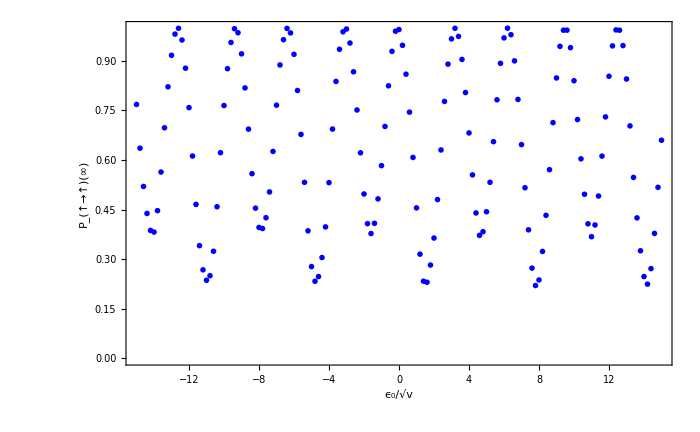

```mathematica
A1=ListPlot[Grid11,PlotRange->All,Axes->None,  Frame->True,FrameLabel->{"ϵ_0/√v","P_(↑→↑)(∞)","",""}, ImageSize->700,PlotMarkers->{-Graphics-,0.04},PlotStyle->{{Black,Thickness[0.005], Dashing[Large]},{Red,Thickness[0.007]},{Red,Thickness[0.005]}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}}]
```

```mathematica
(* We want in this notebook to verify our analyticcal result for Weak Radio-frequency approximation. Analytical yielded:
-Graphics-
where

-Graphics-
and

-Graphics-

and where

-Graphics-

with

-Graphics-

and

-Graphics-

here
-Graphics-

the Landau-Zener paramerers are given by

-Graphics-*)
```

```mathematica
(*-Graphics-*)
Prb1[A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=∑_(j=1)^4 (∑_(j1=1)^4 (P[j,A,A0,ω,Δ,D1,k]P[j1,A,A0,ω,Δ,D1,k]Cos[ζ[j,A,A0,ω,Δ,D1,k,ϕ]-ζ[j1,A,A0,ω,Δ,D1,k,ϕ]]));
(*-Graphics-*)
P[1,A_,A0_,ω_,Δ_,D1_,k_]:=a[1,A,A0,ω,Δ,D1,k] a[2,A,A0,ω,Δ,D1,k] a[3,A,A0,ω,Δ,D1,k];

P[2,A_,A0_,ω_,Δ_,D1_,k_]:=-b[1,A,A0,ω,Δ,D1,k] b[2,A,A0,ω,Δ,D1,k] a[3,A,A0,ω,Δ,D1,k];

P[3,A_,A0_,ω_,Δ_,D1_,k_]:=-a[1,A,A0,ω,Δ,D1,k] b[2,A,A0,ω,Δ,D1,k]b[3,A,A0,ω,Δ,D1,k];

P[4,A_,A0_,ω_,Δ_,D1_,k_]:=-b[1,A,A0,ω,Δ,D1,k] a[2,A,A0,ω,Δ,D1,k] b[3,A,A0,ω,Δ,D1,k];

(*-Graphics-*)
a[1,A_,A0_,ω_,Δ_,D1_,k_]:=√Exp[-(2π delta1[A,A0,ω,Δ,D1,k])/1];

a[2,A_,A0_,ω_,Δ_,D1_,k_]:=√Exp[-(2π delta2[A,A0,ω,Δ,D1,k])/1];

a[3,A_,A0_,ω_,Δ_,D1_,k_]:=√Exp[-(2π delta3[A,A0,ω,Δ,D1,k])/1];

b[1,A_,A0_,ω_,Δ_,D1_,k_]:=√(1-Exp[-(2π delta1[A,A0,ω,Δ,D1,k])/1]);

b[2,A_,A0_,ω_,Δ_,D1_,k_]:=√(1-Exp[-(2π delta2[A,A0,ω,Δ,D1,k])/1]);

b[3,A_,A0_,ω_,Δ_,D1_,k_]:=√(1-Exp[-(2π delta3[A,A0,ω,Δ,D1,k])/1]);

(*-Graphics-*)

delta1[A_,A0_,ω_,Δ_,D1_,k_]:=(A0/(4 √α)BesselJ[k,A/ω])(A0/(4 √α)BesselJ[k,A/ω]);

delta2[A_,A0_,ω_,Δ_,D1_,k_]:=(Δ/(2 √α)BesselJ[k,A/ω])(Δ/(2 √α)BesselJ[k,A/ω]);

delta3[A_,A0_,ω_,Δ_,D1_,k_]:=(A0/(4 √α)BesselJ[k,A/ω])(A0/(4 √α)BesselJ[k,A/ω]);

(*-Graphics-*)

ψ[1,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(omega[1,ω,ω0,D1,k])^2/2+ϕ;

ψ[2,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(omega[2,ω,ω0,D1,k])^2/2;

ψ[3,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(omega[3,ω,ω0,D1,k])^2/2-ϕ;

(*-Graphics-*)

omega[1,ω_,ω0_,D1_,n_]:=D1+n ω-ω0;

omega[2,ω_,ω0_,D1_,n_]:=D1+n ω;

omega[3,ω_,ω0_,D1_,n_]:=D1+n ω+ω0;

(*-Graphics-*)

chi[1,A_,A0_,ω_,Δ_,D1_,k_]:=Pi/4+Arg[Gamma[1-I delta1[A,A0,ω,Δ,D1,k]]]+delta1[A,A0,ω,Δ,D1,k](Log[delta1[A,A0,ω,Δ,D1,k]]-1);

chi[2,A_,A0_,ω_,Δ_,D1_,k_]:=Pi/4+Arg[Gamma[1-I delta2[A,A0,ω,Δ,D1,k]]]+delta2[A,A0,ω,Δ,D1,k](Log[delta2[A,A0,ω,Δ,D1,k]]-1);

chi[3,A_,A0_,ω_,Δ_,D1_,k_]:=Pi/4+Arg[Gamma[1-I delta3[A,A0,ω,Δ,D1,k]]]+delta3[A,A0,ω,Δ,D1,k](Log[delta3[A,A0,ω,Δ,D1,k]]-1);

(*-Graphics-*)

ζ[1,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=0;


ζ[2,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(ψ[2,A,A0,ω,Δ,D1,k,ϕ]-ψ[1,A,A0,ω,Δ,D1,k,ϕ])-(chi[2,A,A0,ω,Δ,D1,k]-chi[1,A,A0,ω,Δ,D1,k]);


ζ[3,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(ψ[2,A,A0,ω,Δ,D1,k,ϕ]-ψ[3,A,A0,ω,Δ,D1,k,ϕ])-(chi[2,A,A0,ω,Δ,D1,k]-chi[3,A,A0,ω,Δ,D1,k]);


ζ[4,A_,A0_,ω_,Δ_,D1_,k_,ϕ_]:=(ψ[1,A,A0,ω,Δ,D1,k,ϕ]-ψ[3,A,A0,ω,Δ,D1,k,ϕ])-(chi[1,A,A0,ω,Δ,D1,k]-chi[3,A,A0,ω,Δ,D1,k]);
```

```mathematica
(*Consider using -Graphics- if necessary*)
```

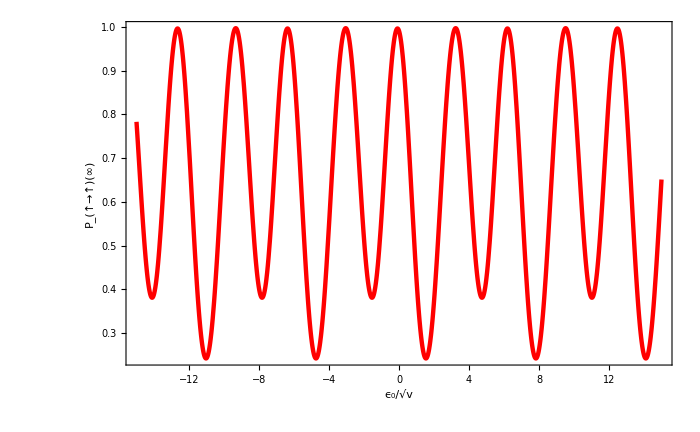

```mathematica
B1=Plot[{Prb1[A,A0,ω,Δ,D1,0,ϕ]},{D1,-15,15},PlotRange->All,Axes->None,  Frame->True,FrameLabel->{"ϵ_0/√v","P_(↑→↑)(∞)","",""}, ImageSize->700,PlotStyle->{{Red,Thickness[0.0045]},{Black,Thickness[0.004], Dashing[Large]},{Blue,Thickness[0.004]},{Blue,Thickness[0.004]},{Red,Thickness[0.004]},{Red,Thickness[0.004]}},LabelStyle->{FontFamily->"Times New Roman",34,GrayLevel[0]},FrameStyle->{{Black,Black},{Black,Black}}]
```

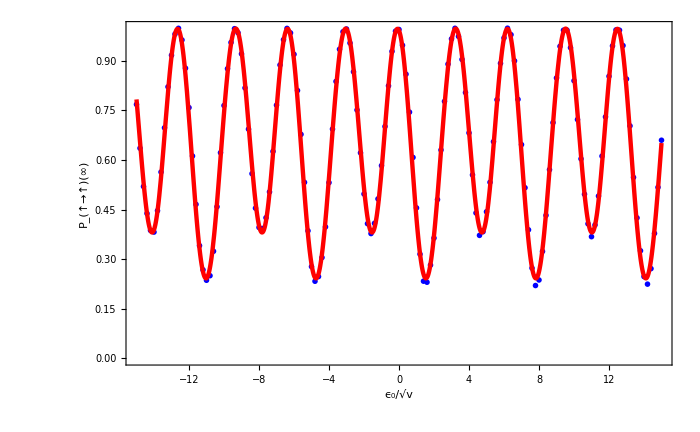

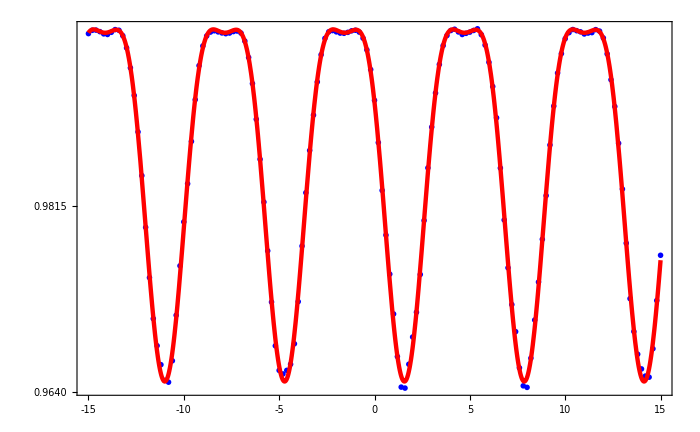

```mathematica
Show[A1,B1]
```